g_μν=(-c^2 (1-(2 μ)/r) | 0 | -(2 a c μ)/r
0 | r^2/(a^2+r^2-2 r μ) | 0
-(2 a c μ)/r | 0 | a^2+r^2+(2 a^2 μ)/r)

g^μν=(-(r^3+a^2 (r+2 μ))/(c^2 r (a^2+r (r-2 μ))) | 0 | -(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ)
0 | (a^2+r^2-2 r μ)/r^2 | 0
-(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ) | 0 | (r-2 μ)/(a^2 r+r^3-2 r^2 μ))

V_eff=(a^2 c^2+h^2-a^2 c^2 k^2)/(2 r^2)-(c^2 μ)/r+(-2 h^2 μ+4 a c h k μ-2 a^2 c^2 k^2 μ)/(2 r^3)

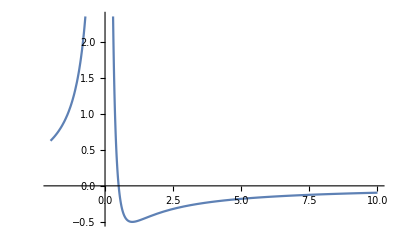

dV/dr=-(a^2 c^2+h^2-a^2 c^2 k^2)/r^3+(c^2 μ)/r^2-(3 (-2 h^2 μ+4 a c h k μ-2 a^2 c^2 k^2 μ))/(2 r^4)

sol1: r=a^2/(2 μ)+h^2/(2 c^2 μ)-(a^2 k^2)/(2 μ)-(√((-a^2 c^2-h^2+a^2 c^2 k^2)^2-4 c^2 μ (3 h^2 μ-6 a c h k μ+3 a^2 c^2 k^2 μ)))/(2 c^2 μ)

sol2: r=a^2/(2 μ)+h^2/(2 c^2 μ)-(a^2 k^2)/(2 μ)+(√((-a^2 c^2-h^2+a^2 c^2 k^2)^2-4 c^2 μ (3 h^2 μ-6 a c h k μ+3 a^2 c^2 k^2 μ)))/(2 c^2 μ)

V_eff=a c k u^2 X+1/2 u (a^2 c^2 u-2 c^2 μ)+1/2 u X^2 (u-2 u^2 μ)

```mathematica
Clear[h,x,V,k,r,ack];
x={t,r,ϕ};
g={{-c^2 (1-2μ/r),0,-2μ a c /r},{0,r^2/(r^2-2μ r+a^2),0},{-2μ a c /r,0,r^2 +a^2+2μ a ^2/r}};
Print["g_μν=",g//MatrixForm];
ginv=FullSimplify[Inverse[g]];
Print["g^μν=",ginv//MatrixForm];
(*
Print["dot{t}=",Simplify[ginv[[1,1]]*(-k c^2)+ginv[[1,3]]*h]];
Print["dot{ϕ}=",Simplify[ginv[[3,1]]*(-k c^2)+ginv[[3,3]]*h]];
*)
V=Collect[Simplify[(c^2+ginv[[1,1]]*(-k c^2)^2+ginv[[3,3]]*h^2+2ginv[[1,3]]*(-k c^2)*h+g[[2,2]]*dr^2)*((r^2+a^2-2 r μ)/(2 r^2))-dr^2/2+(c^2(k^2-1))/2],r];
Print["V_eff=",V];

Print[Plot[V/.{a->1,c->1,k->1,h->1,μ->1},{r,-2,10}]];

dV=D[V,r];
Print["dV/dr=",dV];
sol=Solve[{dV==0},r];

Print["sol1: r=",Expand[r/.sol[[1]]]];
Print["sol2: r=",Expand[r/.sol[[2]]]];

h=X+a c k;
r=1/u;

Print["V_eff=",Collect[Simplify[V],X]];

(*
eqn=V-(c^2(k^2-1))/2;

sol=Solve[{eqn==0},X];

Print["sol1: X^2=",Collect[Expand[(X/.sol[[1]])^2],u]];
Print["sol2: X^2=",Collect[Expand[(X/.sol[[2]])^2],u]];
*)

(*
Γ=Table[(1/2)*Sum[ginv[[i,l]](D[g[[l,j]],x[[k]]]+D[g[[l,k]],x[[j]]]-D[g[[j,k]],x[[l]]]),{l,1,3}],{i,1,3},{j,1,3},{k,1,3}];

Do[
Print["Γ[",x[[i]],",",x[[j]],",",x[[k]],"]=",Γ[[i,j,k]]];
,{i,1,3},{j,1,3},{k,1,3}]
*)
```

```mathematica
x={t,r,θ,ϕ};
g={{-c^2 (1-2μ r/(r^2+a^2Cos[θ]^2)),0,0,-2μ a c r Sin[θ]^2/(r^2+a^2Cos[θ]^2)},{0,(r^2+a^2Cos[θ]^2)/(r^2-2μ r+a^2),0,0},{0,0,r^2+a^2Cos[θ]^2,0},{-2μ a c r Sin[θ]^2/(r^2+a^2Cos[θ]^2),0,0,r^2 +a^2+2μ r a ^2 Sin[θ]^2/(r^2+a^2Cos[θ]^2)}};

ginv=FullSimplify[Inverse[g]];

g=g/.θ->Pi/2;
ginv=FullSimplify[ginv/.θ->Pi/2];
Print["g_μν=",g//MatrixForm];
Print["g^μν=",ginv//MatrixForm];
```

g_μν=(-c^2 (1-(2 μ)/r) | 0 | 0 | -(2 a c μ)/r
0 | r^2/(a^2+r^2-2 r μ) | 0 | 0
0 | 0 | r^2 | 0
-(2 a c μ)/r | 0 | 0 | a^2+r^2+(2 a^2 μ)/r)

g^μν=(-(r^3+a^2 (r+2 μ))/(c^2 r (a^2+r (r-2 μ))) | 0 | 0 | -(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ)
0 | (a^2+r^2-2 r μ)/r^2 | 0 | 0
0 | 0 | 1/r^2 | 0
-(2 a μ)/(a^2 c r+c r^3-2 c r^2 μ) | 0 | 0 | 1/(r (r+a^2/(r-2 μ))))